## Initialization

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Libraries\_Git Public\Wolfram-Mathematica

```mathematica
Needs["SuperPackage`"]
```

```mathematica
SetΔ0[200 1.6 10^-25];
Setγ[10^-4];
SetvF[2.3 10^6];

Tc = GetΔ0[]/(1.764*kB); (*Real value of the BCS critical temperature*)
ξ0=(* 1/Δ0 *) ℏ*GetvF[]; (*ξ0 is rescaled by Δ0, which causes the Δ0 to drop out. This rescaled ξ0 is thus in units of m×Δ0*)
```

```mathematica
{GetΔ0[],GetTc[],Getγ[],GetvF[]}
```

{3.2×10^-23,1.31401[],1/10000,2.3×10^6}

## General plots

### Global parameters defined in SuperPackage

```mathematica
{kB,q,Φ0,h,ℏ}
```

{1.38065×10^-23,1.60218×10^-19,2.067×10^-15,6.62607×10^-34,1.05457×10^-34}

### Superconducting gap

```mathematica
?Δ
```

Δ[T] 
 Gives the gap.

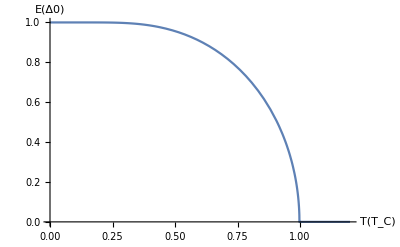

```mathematica
Plot[Δ[x],{x,0,1.2},AxesLabel->{"T(T_C)","E(Δ0)"}]
```

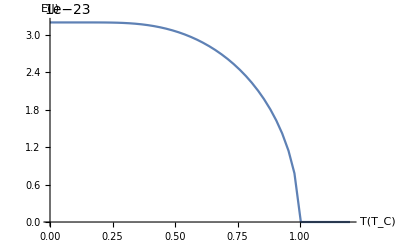

```mathematica
Plot[Δ[x,rescale -> False],{x,0,1.2},AxesLabel->{"T(T_C)","E(J)"}]
```

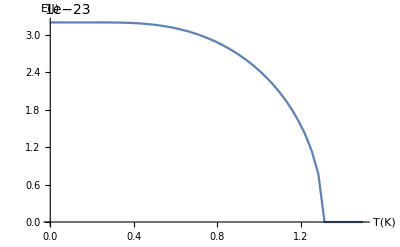

```mathematica
Plot[Δ[(x/Tc) ,rescale -> False],{x,0,1.5},AxesLabel->{"T(K)","E(J)"}]
```

### Fermi function

```mathematica
Information["fermi",LongForm->False]
```

fermi[energy,T] 
 The Fermi districution function.

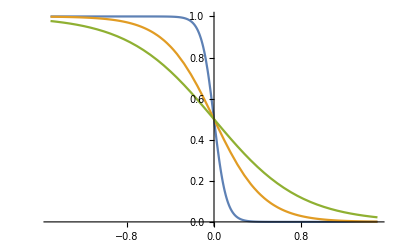

```mathematica
Plot[{fermi[x,0.1],fermi[x,0.4],fermi[x,0.7]},{x,-1.5,1.5}]
```

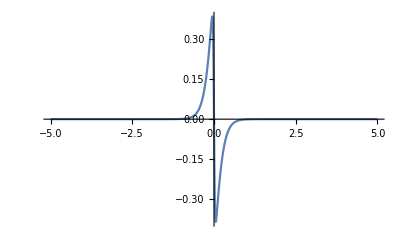

```mathematica
Plot[fermi[energy,0.025]-fermi[energy,0.25],{energy,-5,5},PlotRange->Full]
```

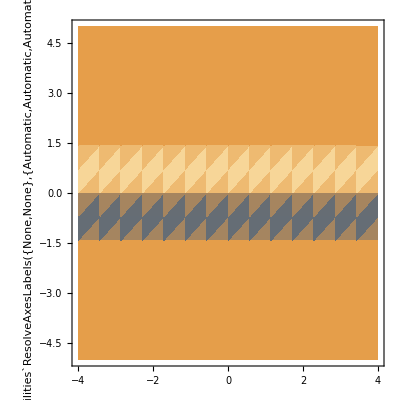

```mathematica
DensityPlot[fermi[energy,0.25]-fermi[energy,0.025],{x,-4,4},{energy,-5,5},PlotRange->Full]
```

With a voltage bias

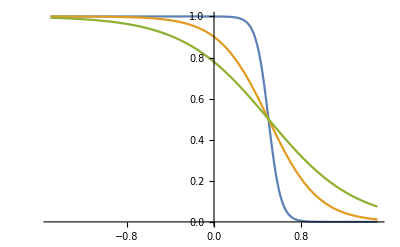

```mathematica
Module[{V=0.5},Plot[{fermi[energy-V,0.1],fermi[energy-V,0.4],fermi[energy-V,0.7]},{energy,-1.5,1.5}]]
```

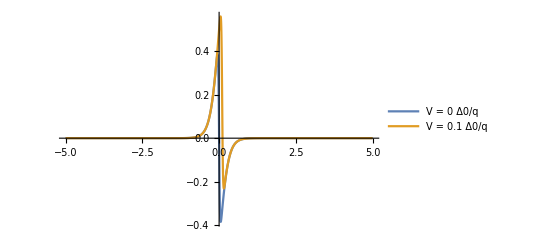

```mathematica
Plot[{fermi[energy+0,0.025]-fermi[energy,0.25],fermi[energy-0.1,0.025]-fermi[energy,0.25]},{energy,-5,5},PlotRange->Full,PlotLegends->{"V = 0 \!\(\*FractionBox[\(Δ0\), \(q\)]\)","V = 0.1 \!\(\*FractionBox[\(Δ0\), \(q\)]\)"}]
```

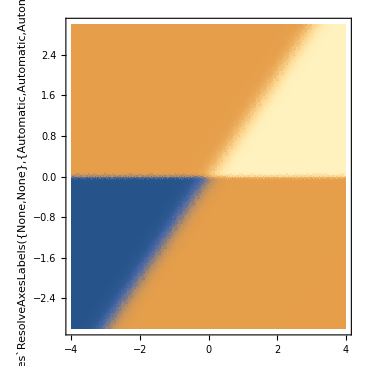
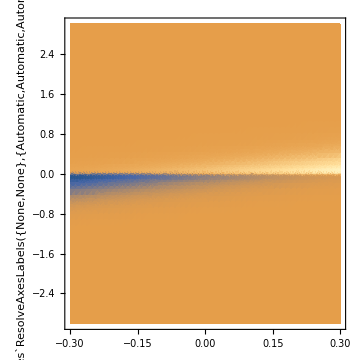

```mathematica
{DensityPlot[fermi[energy-V,0.25]-fermi[energy,0.025],{V,-4,4},{energy,-3,3},PlotRange->Full,PlotPoints->50],DensityPlot[fermi[energy-V,0.25]-fermi[energy,0.025],{V,-0.3,0.3},{energy,-3,3},PlotRange->Full,PlotPoints->50]}
```

### Quasi-particle density of states

```mathematica
?ρQP
```

ρQP[energy,T] 
 The BCS quasiparticle density of states.

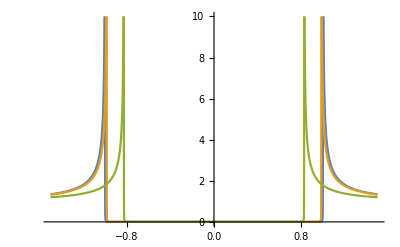

```mathematica
Plot[{ρQP[x,0.1],ρQP[x,0.4],ρQP[x,0.7]},{x,-1.5,1.5},PlotRange->{0,10}]
```

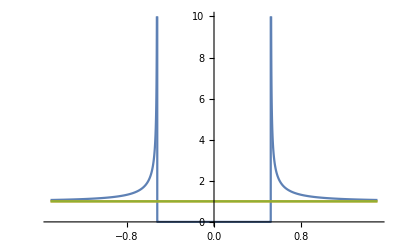

```mathematica
Plot[{ρQP[x,0.9],ρQP[x,1.2],ρQP[x,1.5]},{x,-1.5,1.5},PlotRange->{0,10}]
```

### Transmission of a topological Josephson junction

```mathematica
?transmissionTJJ
```

transmissionTJJ[energy, flux, T, L, ϕ0:0] 
 The transmission function of a topological Josepson junction not including the Andreev bound states. The length is expected in units of ξ0 (which is itself rescaled by Δ0). The superconducting phase difference ϕ0 is optional, and 0 by default.

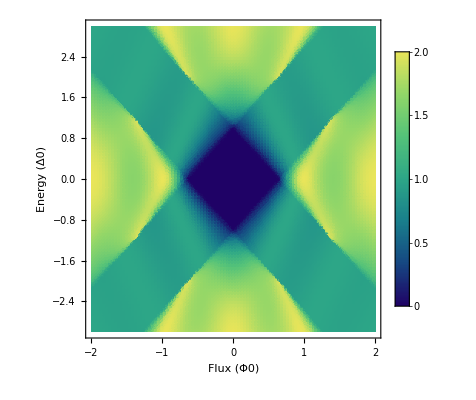

```mathematica
DensityPlot[transmissionTJJ[energy,flux,0.1,1 ξ0],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)","Transmission"}]
```

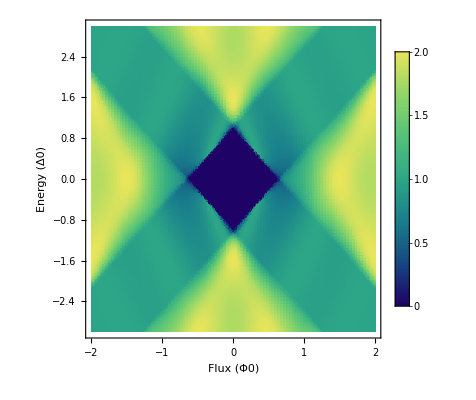

```mathematica
DensityPlot[transmissionTJJ[energy,flux,0.1,1 ξ0, Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)","Transmission"},PlotRange->2]
```

#### Individial edges

```mathematica
?transmissionTJJU
```

transmissionTJJ[energy, flux, T, L, ϕ0:0] 
 The transmission function of a topological Josepson junction for right-moving particles along the upper edge, not including the Andreev bound states. The length is expected in units of ξ0 (which is itself rescaled by Δ0). The superconducting phase difference ϕ0 is optional, and 0 by default.

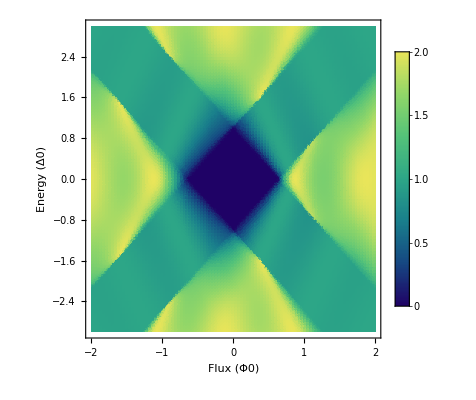

```mathematica
DensityPlot[transmissionTJJU[energy,flux,0.1,1 ξ0,0.25 Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)","Transmission"}]
```

```mathematica
?transmissionTJJL
```

transmissionTJJ[energy, flux, T, L, ϕ0:0] 
 The transmission function of a topological Josepson junction for right-moving particles along the lower edge, not including the Andreev bound states. The length is expected in units of ξ0 (which is itself rescaled by Δ0). The superconducting phase difference ϕ0 is optional, and 0 by default.

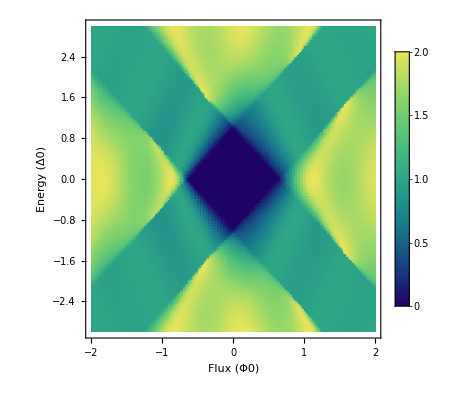

```mathematica
DensityPlot[transmissionTJJL[energy,flux,0.1,1 ξ0,0.25 Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)","Transmission"}]
```

### Topological Josephson junction density of states, without ABS

```mathematica
?ρTJJ
```

ρTJJ[energy, flux, T, L, ϕ0:0] 
 The density of states of a topological Josephson junction, not including the Andreev bound states. The length is expected in units of ξ0 (which is itself rescaled by Δ0). The superconducting phase difference ϕ0 is optional, and 0 by default.

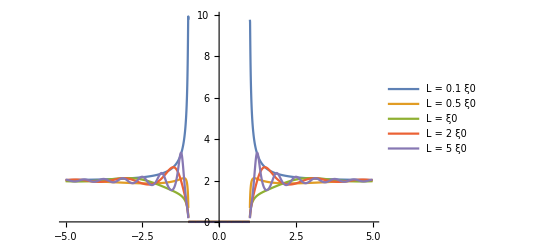

```mathematica
Plot[{ρTJJ[energy,0,0.1,0.1ξ0],ρTJJ[energy,0,0.1,0.5ξ0],ρTJJ[energy,0,0.1,ξ0],ρTJJ[energy,0,0.1,2ξ0],ρTJJ[energy,0,0.1,5ξ0]},{energy,-5,5},PlotRange->Full,PlotLegends->{"L = 0.1 ξ0","L = 0.5 ξ0","L =  ξ0","L = 2 ξ0","L = 5 ξ0"}]
```

#### Comparison with NIS junction

```mathematica
?ρQP
```

ρQP[energy,T] 
 The BCS quasiparticle density of states.

#### Density plots

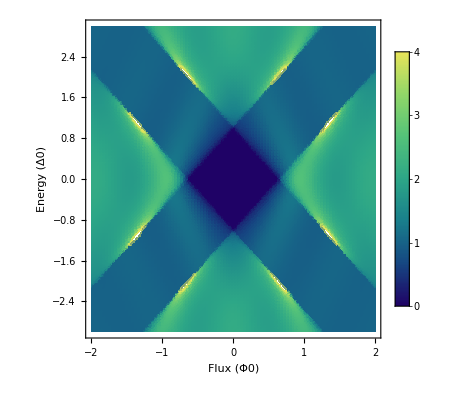

```mathematica
DensityPlot[ρTJJ[energy,flux,0.1,1 ξ0],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotRange->4,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)"}]
```

#### ϕ0 dependency

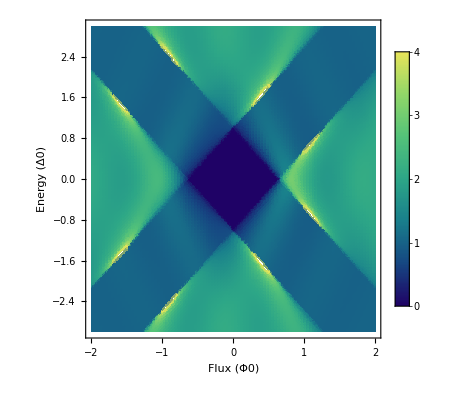
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{DensityPlot[ρTJJ[energy,flux,0.1,1 ξ0,0Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotRange->4,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)"}],
DensityPlot[ρTJJ[energy,flux,0.1,1 ξ0,0.25Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotRange->4,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)"}],
DensityPlot[ρTJJ[energy,flux,0.1,1 ξ0,0.5Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotRange->4,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)"}],
DensityPlot[ρTJJ[energy,flux,0.1,1 ξ0,.75Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotRange->4,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)"}],
DensityPlot[ρTJJ[energy,flux,0.1,1 ξ0,Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotRange->4,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)"}],
DensityPlot[ρTJJ[energy,flux,0.1,1 ξ0,1.25Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotRange->4,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)"}],
DensityPlot[ρTJJ[energy,flux,0.1,1 ξ0,1.5Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotRange->4,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)"}],
DensityPlot[ρTJJ[energy,flux,0.1,1 ξ0,1.75Pi],{flux,-2,2},{energy,-3,3},Exclusions->None,ColorFunction->"BlueGreenYellow",PlotPoints->100,PlotRange->4,PlotLegends->Automatic,FrameLabel->{ "Flux (Φ0)","Energy (Δ0)"}]}
```

## Thermal transport Normal probe

### JNIS

```mathematica
?JNIS
```

JNIS[tempN, tempS, γ:0, RTunnelProbe:1, rescale -> True] 
 The heat current through an NIS tunnel junction.

```mathematica
JNIS[0.025,0.9]
```

-0.455414

```mathematica
{Plot[JNIS[0.025,TempS],{TempS,0.025,2}],Plot[JNIS[TempN,0.025],{TempN,0.025,2}]}
```

{-Graphics-,-Graphics-}

```mathematica
{DensityPlot[JNIS[TNormal,TSuper],{TNormal,0.025,2},{TSuper,0.025,2},FrameLabel->{"TNormal (T_C)","TSuper (T_C)"},PlotLegends->Automatic],Plot3D[JNIS[TNormal,TSuper],{TNormal,0.025,2},{TSuper,0.025,2},AxesLabel->{"TNormal (T_C)","TSuper (T_C)"},PlotLegends->Automatic]}
```

{-Graphics-,-Graphics3D-}

#### Rectification coefficients JNIS

Replication of the NIS plot in Fig. 1 of the “Efficient phase-tunable Josephson thermal rectifier” paper, doi: 10.1063/1.4804550

```mathematica
Plot[{rectCoefficientRelative[JNIS[T1,T2],T1,T2,0.01,Thot],
rectCoefficientRelative[JNIS[T1,T2],T1,T2,0.3,Thot],
rectCoefficientRelative[JNIS[T1,T2],T1,T2,0.4,Thot],
rectCoefficientRelative[JNIS[T1,T2],T1,T2,0.5,Thot],
rectCoefficientRelative[JNIS[T1,T2],T1,T2,0.6,Thot],
rectCoefficientRelative[JNIS[T1,T2],T1,T2,0.7,Thot]},{Thot,0.01,2},AxesLabel->{"THot (T_C)","R (%)"},PlotLegends->{"TCold = 0.01 T_C","TCold = 0.3 T_C","TCold = 0.4 T_C","TCold = 0.5 T_C","TCold = 0.6 T_C","TCold = 0.7 T_C"}]
```

-Graphics-

```mathematica
Module[{gamma = 10^-5},Plot[{rectCoefficientRelative[JNIS[T1,T2],T1,T2,0.01,Thot],
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,0.3,Thot],
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,0.5,Thot],
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,0.7,Thot],
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,0.9,Thot],
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,1.1,Thot]},{Thot,0.01,2},AxesLabel->{"THot (T_C)","R (%)"},PlotLegends->{"TCold = 0.01 T_C","TCold = 0.3 T_C","TCold = 0.5 T_C","TCold = 0.7 T_C","TCold = 0.9 T_C","TCold = 1.1 T_C"}]]
```

-Graphics-

Inverse definition (T1 and T2 reversed)

```mathematica
Module[{gamma = 10^-5},Plot[{rectCoefficientRelative[JNIS[T1,T2],T1,T2,Thot,0.01],
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,Thot,0.3],
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,Thot,0.4],
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,Thot,0.5],
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,Thot,0.6],
rectCoefficientRelative[JNIS[T1,T2,gamma],T1,T2,Thot,0.7]},{Thot,0.01,2},AxesLabel->{"THot (T_C)","R (%)"},PlotLegends->{"TCold = 0.01 T_C","TCold = 0.3 T_C","TCold = 0.4 T_C","TCold = 0.5 T_C","TCold = 0.6 T_C","TCold = 0.7 T_C"}]]
```

-Graphics-

### Thermal conductance TJJ

```mathematica
?thermalConductanceTJJ
```

thermalConductanceTJJ[flux_,T_,L_,ϕ0:0,rescale -> True (False)] 
 The thermal conductance of a topological Josephson junction, in the linear approximation. When setting rescale -> False, a value for ϕ0 must be provided.

```mathematica
{thermalConductanceTJJ[1,0.1,1 ξ0],
thermalConductanceTJJ[1,0.1,1 ξ0, 0],
thermalConductanceTJJ[1,0.1,1 ξ0, 0,rescale -> True],
thermalConductanceTJJ[1,0.1,1 ξ0,0,rescale -> False]}
```

{0.202978,0.202978,0.202978,2.38723×10^-13}

```mathematica
?GQ
```

GQ[T] 
 The quantum of thermal conductance. Input T is expected in units of Tc, as per usual.

```mathematica
GQ[0.1]
```

9.46433×10^-14

```mathematica
Plot[{thermalConductanceTJJ[flux,0.1,ξ0,0,rescale->False]/GQ[0.1 ],thermalConductanceTJJ[flux,0.2,ξ0,0,rescale->False]/GQ[0.2 ],thermalConductanceTJJ[flux,0.4,ξ0,0,rescale->False]/GQ[0.4 ]},{flux,-5,5 },PlotLegends -> {"T = 0.1 K","T = 0.2 K","T = 0.4 K"},PlotLabel->"Thermal conductance for L = ξ0 and ϕ0 = 0, in units of the thermal conductance quantum"]
```

-Graphics-

```mathematica
Plot[{thermalConductanceTJJ[flux,0.1,ξ0],thermalConductanceTJJ[flux,0.2,ξ0],thermalConductanceTJJ[flux,0.4,ξ0]},{flux,-5 ,5 },PlotLegends -> {"T = 0.1 K","T = 0.2 K","T = 0.4 K"},PlotLabel->"Thermal conductance for L = ξ0 and ϕ0 = 0"]
```

-Graphics-

```mathematica
Plot[{thermalConductanceTJJ[flux,0.1,3ξ0]/GQ[0.1],thermalConductanceTJJ[flux,0.2,3ξ0]/GQ[0.2],thermalConductanceTJJ[flux,0.4,3ξ0]/GQ[0.4],thermalConductanceTJJ[flux,0.6,3ξ0]/GQ[0.6],thermalConductanceTJJ[flux,0.8,3ξ0]/GQ[0.8]},{flux,-10 ,10 },PlotLegends -> {"T = 0.1 K","T = 0.2 K","T = 0.4 K","T = 0.6 K","T = 0.8 K"},PlotLabel->"Thermal conductance for L = 3ξ0 and ϕ0 = 0, in units of the thermal conductance quantum",PlotRange->Automatic]
```

-Graphics-

```mathematica
Plot3D[thermalConductanceTJJ[flux,0.1,1 ξ0](ΔT),{ΔT,0,1},{flux,0,2.5},AxesLabel->{"ΔT","Flux","JJunction"}, PlotLegends -> {"T TI = 0.1 Tc"}]
```

-Graphics3D-

#### thermalConductanceTJJ rescaling check

```mathematica
Module[{T=0.1,L=ξ0,ϕ0=0,Δ0 = 200 1.6 10^-25},
Plot[{thermalConductanceTJJ[flux,0.1,1 ξ0,0,rescale -> False],1/h NIntegrate[(energy^2 transmissionTJJ[energy/Δ0,flux,T,L,ϕ0])/(4kB T^2 Tc^2 Cosh[energy/(2 kB T Tc)]^2),{energy,-10Δ0,10Δ0},MaxRecursion->25,MinRecursion->5,AccuracyGoal->10,Method->Oscillatory]},{flux,0,3}]]
-Graphics-
```

```mathematica
Module[{flux=0.34,L=ξ0,ϕ0=0,Δ0 = 200 1.6 10^-25},
Plot[{thermalConductanceTJJ[flux,T,1 ξ0,0,rescale -> False],1/h NIntegrate[(energy^2 transmissionTJJ[energy/Δ0,flux,T ,L,ϕ0])/(4kB T^2 Tc^2 Cosh[energy/(2 kB T Tc)]^2),{energy,-10Δ0,10Δ0},MaxRecursion->25,MinRecursion->5,AccuracyGoal->10,Method->Oscillatory]},{T,0.1,.8}]]
```

-Graphics-

### Nonlinear heat current through a TJJ

```mathematica
?JJunctionNonLinear
```

JJunctionNonLinear [flux, Ts1, Ts2, L, ϕ0:0, rescale -> True (False)] 
 The (non linear) heat current through a topological Josephson junction.

```mathematica
Module[{Ts1=0.5,Ts2 = 0.025,L=ξ0},
Plot[{JJunctionLinear[flux,Ts1,Ts2,L],JJunctionNonLinear[flux,Ts1,Ts2,L]},{flux,-4,4}]]
```

-Graphics-

```mathematica
Module[{Ts2 = 0.025,L=ξ0,plotOptions = {ImageSize -> Medium,AxesLabel->{"Flux (Φ0)","J (Δ_0^2/h)"},PlotLegends-> {"J linear","J nonlinear"}}},
{Plot[{JJunctionLinear[flux,0.1,Ts2,L],JJunctionNonLinear[flux,0.1,Ts2,L]},{flux,-4,4},Evaluate[plotOptions]],
Plot[{JJunctionLinear[flux,0.5,Ts2,L],JJunctionNonLinear[flux,0.5,Ts2,L]},{flux,-4,4},Evaluate[plotOptions]],
Plot[{JJunctionLinear[flux,0.9,Ts2,L],JJunctionNonLinear[flux,0.9,Ts2,L]},{flux,-4,4},Evaluate[plotOptions]]}]
```

{-Graphics-,-Graphics-,-Graphics-}

### GNProbe

```mathematica
?GNProbe
```

GNProbeLinear[flux, T, L, ϕ0:0, V:0 ,RTunnelProbe:1, rescale -> True] 
 The thermal conductance of a normal probe - TJJ.

```mathematica
GNProbe[0, 0.1, ξ0]
```

3.60585×10^-7

```mathematica
GNProbe[0, 0.1, ξ0,0,0,1,rescale -> False]
```

1.09469×10^-14

```mathematica
Plot[GNProbe[0, T, ξ0],{T,0.1,2}]
```

-Graphics-

```mathematica
Plot[GNProbe[0, 0.1, L ξ0],{L,0.1,5}]
```

-Graphics-

```mathematica
Plot[GNProbe[flux, 0.1, ξ0],{flux,-4,4}]
```

-Graphics-

```mathematica
{Plot[{thermalConductanceTJJ[flux,0.1,ξ0],thermalConductanceTJJ[flux,0.2,ξ0],thermalConductanceTJJ[flux,0.4,ξ0],thermalConductanceTJJ[flux,0.6,ξ0],thermalConductanceTJJ[flux,0.8,ξ0],thermalConductanceTJJ[flux,1,ξ0]},{flux,-5,5 },PlotLegends -> {"T = 0.1 Tc","T = 0.2 Tc","T = 0.4 Tc","T = 0.6 Tc","T = 0.8 Tc","T = 1 Tc"},PlotLabel->"Thermal conductance (Expression Björn) for L = ξ0 and ϕ0 = 0, in rescaled units"],
Plot[{GNProbe[flux,0.1,ξ0],GNProbe[flux,0.2,ξ0 ],GNProbe[flux,0.4,ξ0 ],GNProbe[flux,0.6,ξ0 ],GNProbe[flux,0.8,ξ0 ],GNProbe[flux,1,ξ0 ]},{flux,-5,5 },PlotLegends -> {"T = 0.1 Tc","T = 0.2 Tc","T = 0.4 Tc","T = 0.6 Tc","T = 0.8 Tc","T = 1 Tc"},PlotLabel->"Thermal conductance (GNProbe) for L = ξ0 and ϕ0 = 0, in units of the thermal conductance quantum / R_T"]}
```

{-Graphics-,-Graphics-}

```mathematica
{Plot[{thermalConductanceTJJ[flux,0.1,ξ0,0,rescale->False]/GQ[0.1 ],thermalConductanceTJJ[flux,0.2,ξ0,0,rescale->False]/GQ[0.2 ],thermalConductanceTJJ[flux,0.4,ξ0,0,rescale->False]/GQ[0.4 ]},{flux,-5,5 },PlotLegends -> {"T = 0.1 K","T = 0.2 K","T = 0.4 K"},PlotLabel->"Thermal conductance (Expression Björn) for L = ξ0 and ϕ0 = 0, in units of the thermal conductance quantum"],
Plot[{GNProbe[flux,0.1,ξ0,0,0,25812.81079353287,rescale->False]/GQ[0.1 ],GNProbe[flux,0.2,ξ0,0,0,25812.81079353287,rescale->False]/GQ[0.2 ],GNProbe[flux,0.4,ξ0,0,0,25812.81079353287,rescale->False]/GQ[0.4 ]},{flux,-5,5 },PlotLegends -> {"T = 0.1 K","T = 0.2 K","T = 0.4 K"},PlotLabel->"Thermal conductance (GNProbe) for L = ξ0 and ϕ0 = 0, in units of the thermal conductance quantum / R_T"]}
```

{-Graphics-,-Graphics-}

```mathematica
{Plot[{GNProbe[flux,0.1,ξ0]/GNProbe[4,0.1,ξ0],GNProbe[flux,0.2,ξ0]/GNProbe[4,0.2,ξ0],GNProbe[flux,0.4,ξ0]/GNProbe[4,0.4,ξ0]},{flux,-4,4 },PlotLegends -> {"T = 0.1 K","T = 0.2 K","T = 0.4 K"},PlotLabel->"Thermal conductance (GNProbe) for L = ξ0 and ϕ0 = 0, in units of GNProbe[4,T,ξ0]"],
Plot[{GNProbe[flux,0.1,ξ0]/GNProbe[4,1,ξ0],GNProbe[flux,0.2,ξ0]/GNProbe[4,1,ξ0],GNProbe[flux,0.4,ξ0]/GNProbe[4,1,ξ0]},{flux,-4,4 },PlotLegends -> {"T = 0.1 K","T = 0.2 K","T = 0.4 K"},PlotLabel->"Thermal conductance (GNProbe) for L = ξ0 and ϕ0 = 0, in units of GNProbe[4,T_C,ξ0]"]}
```

{-Graphics-,-Graphics-}

### JNProbe: heat current between a N probe and a TJJ

```mathematica
?JNProbe
```

JNProbe[flux, tempNProbe, tempJunction, L, ϕ0:0, RTunnelProbe:1, rescale -> True (False)] 
 The heat current between a normal metal probe, tunnel coupled to one side of a topological Josephson junction. The length is expected in units of ξ0 (which is itself rescaled by Δ0). Can be descaled using rescale -> False as the last argument, in this case ϕ0 and RTunnelProbe must be provided.

```mathematica
{JNProbe[0,0.5,0.1,1 ξ0],JNProbe[0,0.5,0.1,1 ξ0,0,0,10000],JNProbe[0,0.5,0.1,1 ξ0,0,0,10000,rescale->True],JNProbe[0,0.5,0.1,1 ξ0,0,0,10000,rescale->False]}
```

{0.0261171,0.0261171,0.0261171,1.04185×10^-13}

#### JNProbe integrand

Low temperatures

```mathematica
Module[{tempJunction = 0.025,tempNProbe = 0.25,L=ξ0,ϕ0=0,plotOptions ={Exclusions->None,PlotPoints->50,ImageSize -> Medium ,PlotLegends ->Automatic, FrameLabel->{"Flux (Φ0)","Energy (Δ0)"}}},
{DensityPlot[ ρTJJ[energy,flux,tempJunction,L,ϕ0],{flux,-4,4},{energy,-10,10},Evaluate[plotOptions] ],
DensityPlot[(fermi[energy,tempNProbe]-fermi[energy,tempJunction]),{flux,-4,4},{energy,-2,2},Evaluate[plotOptions],PlotRange->Full],
DensityPlot[energy * ρTJJ[energy,flux,tempJunction,L,ϕ0],{flux,-4,4},{energy,-10,10},Evaluate[plotOptions]],
DensityPlot[energy * ρTJJ[energy,flux,tempJunction,L,ϕ0]*(fermi[energy,tempNProbe]-fermi[energy,tempJunction]),{flux,-4,4},{energy,-2,2},Evaluate[plotOptions],PlotRange->Full]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

High temperatures

```mathematica
Module[{tempJunction = 0.025,tempNProbe = 0.9,L=ξ0,ϕ0=0,plotOptions ={Exclusions->None,PlotPoints->50,ImageSize -> Medium ,PlotLegends ->Automatic, FrameLabel->{"Flux (Φ0)","Energy (Δ0)"}}},
{DensityPlot[ ρTJJ[energy,flux,tempJunction,L,ϕ0],{flux,-4,4},{energy,-10,10},Evaluate[plotOptions] ],
DensityPlot[(fermi[energy,tempNProbe]-fermi[energy,tempJunction]),{flux,-4,4},{energy,-2,2},Evaluate[plotOptions],PlotRange->Full],
DensityPlot[energy * ρTJJ[energy,flux,tempJunction,L,ϕ0],{flux,-4,4},{energy,-10,10},Evaluate[plotOptions]],
DensityPlot[energy * ρTJJ[energy,flux,tempJunction,L,ϕ0]*(fermi[energy,tempNProbe]-fermi[energy,tempJunction]),{flux,-4,4},{energy,-2,2},Evaluate[plotOptions],PlotRange->Full]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Integrand for different superconducting phase differences

```mathematica
Module[{tempJunction = 0.025,tempNProbe = 0.25,L=ξ0,plotOptions ={Exclusions->None,PlotPoints->50,PlotRange->{0,0.2},ImageSize -> Medium ,PlotLegends ->Automatic, FrameLabel->{"Flux (Φ0)","Energy (Δ0)"}}},
{DensityPlot[energy * ρTJJ[energy,flux,tempJunction,L,0]*(fermi[energy,tempNProbe]-fermi[energy,tempJunction]),{flux,-4,4},{energy,-2,2},Evaluate[plotOptions]],
DensityPlot[energy * ρTJJ[energy,flux,tempJunction,L,.5Pi]*(fermi[energy,tempNProbe]-fermi[energy,tempJunction]),{flux,-4,4},{energy,-2,2},Evaluate[plotOptions]],
DensityPlot[energy * ρTJJ[energy,flux,tempJunction,L,Pi]*(fermi[energy,tempNProbe]-fermi[energy,tempJunction]),{flux,-4,4},{energy,-2,2},Evaluate[plotOptions]],
DensityPlot[energy * ρTJJ[energy,flux,tempJunction,L,1.5Pi]*(fermi[energy,tempNProbe]-fermi[energy,tempJunction]),{flux,-4,4},{energy,-2,2},Evaluate[plotOptions]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### JNProbe plots

```mathematica
{Plot[{JNProbe[flux,0.25,0.025,ξ0],-JNProbe[flux,0.025,0.25,ξ0]},{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J (Δ0^2/q^2)"},ImageSize->Medium],Plot[{JNProbe[flux,0.8,0.025,ξ0],-JNProbe[flux,0.025,0.8,ξ0]},{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J (Δ0^2/q^2)"},ImageSize->Medium],Plot[{JNProbe[flux,0.9,0.025,ξ0],-JNProbe[flux,0.025,0.9,ξ0]},{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J (Δ0^2/q^2)"},ImageSize->Medium]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Plot[{JNProbe[flux,1.,0.025,ξ0],-JNProbe[flux,0.025,1.,ξ0]},{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J (Δ0^2/q^2)"},ImageSize->Medium,PlotRange->Full],Plot[{JNProbe[flux,1.5,0.025,ξ0],-JNProbe[flux,0.025,1.5,ξ0]},{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J (Δ0^2/q^2)"},ImageSize->Medium],Plot[{JNProbe[flux,2.,0.025,ξ0],-JNProbe[flux,0.025,2.,ξ0]},{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J (Δ0^2/q^2)"},ImageSize->Medium]}
```

{-Graphics-,-Graphics-,-Graphics-}

#### JNProbe plots with various ϕ0

```mathematica
Module[{tempJunction = 0.025,tempNProbe = 0.9,L=ξ0,ϕ0=0,plotOptions ={Exclusions->None,ImageSize -> Medium ,PlotLegends ->Automatic, AxesLabel->{"Flux (Φ0)","J (Δ0^2/q^2)"}}},
{Plot[{JNProbe[flux,0.9,0.025,ξ0],-JNProbe[flux,0.025,0.9,ξ0]},{flux,-4,4},Evaluate[plotOptions]],
Plot[{JNProbe[flux,0.9,0.025,ξ0,.5Pi],-JNProbe[flux,0.025,0.9,ξ0,.5Pi]},{flux,-4,4},Evaluate[plotOptions]],
Plot[{JNProbe[flux,0.9,0.025,ξ0,Pi],-JNProbe[flux,0.025,0.9,ξ0,Pi]},{flux,-4,4},Evaluate[plotOptions]],
Plot[{JNProbe[flux,0.9,0.025,ξ0,1.5Pi],-JNProbe[flux,0.025,0.9,ξ0,1.5Pi]},{flux,-4,4},Evaluate[plotOptions]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot3D[JNProbe[flux,0.9,0.025,ξ0,phase],{flux,-4,4},{phase,-4Pi,4Pi}]
```

-Graphics3D-

```mathematica
DensityPlot[JNProbe[flux,0.9,0.025,ξ0,phase Pi],{flux,-4,4},{phase,0,2}]
```

-Graphics-

```mathematica
Plot[{JNProbe[flux,0.9,0.025,ξ0],JNProbe[flux,0.9,0.025,ξ0,.5Pi],JNProbe[flux,0.9,0.025,ξ0,Pi],JNProbe[flux,0.9,0.025,ξ0,1.5Pi]},{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J (Δ0^2/q^2)"}]
```

-Graphics-

### Rectification coefficients general

```mathematica
?rectCoefficientRatio
```

rectCoefficientRatio[f[..., T1, T2,...], T1, T2, THot, TCold] 
 The rectification coefficient defined as -J_forward/J_backward. The first argument is the expession for J that is to be used. The variables for temperature (T1,T2) must be consistent!

```mathematica
?rectCoefficientRelative
```

rectCoefficientRelative[f[..., T1, T2,...],T1, T2 THot, TCold] 
 The rectification coefficient defined as 100 (J_forward-J_backward)/J_backward. The first argument is the expession for J that is to be used. The variables for temperature (T1,T2) must be consistent!

```mathematica
rectCoefficientRatio[JNProbe[0,T1,T2,ξ0],T1,T2,0.025,0.9]//Timing
```

{0.015625,2.08783}

```mathematica
{Plot[rectCoefficientRatio[JNProbe[flux,T1,T2,ξ0],T1,T2,0.025,0.9],{flux,-3,3},PlotRange->Full],Plot[rectCoefficientRelative[JNProbe[flux,T1,T2,ξ0],T1,T2,0.025,0.9],{flux,-3,3},PlotRange->Full]}
```

{-Graphics-,-Graphics-}

```mathematica
Plot[-rectCoefficientRelative[JNProbe[flux,T1,T2,ξ0],T1,T2,0.9,0.025],{flux,-3,3},PlotRange->Full]
```

-Graphics-

```mathematica
{Plot[{rectCoefficientRelative[JNProbe[flux,T1,T2,0.5ξ0],T1,T2,0.025,0.9],rectCoefficientRelative[JNProbe[flux,T1,T2,ξ0],T1,T2,0.025,0.9],rectCoefficientRelative[JNProbe[flux,T1,T2,2ξ0],T1,T2,0.025,0.9],rectCoefficientRelative[JNProbe[flux,T1,T2,3ξ0],T1,T2,0.025,0.9]},{flux,-3,3},PlotRange->Full]}
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{-Graphics-}

```mathematica
Block[{tab},
tab=Flatten[Table[{flux,L,rectCoefficientRelative[JNProbe[flux,T1,T2,L ξ0],T1,T2,0.01,0.9]},{flux,-3,3,0.1},{L,0.01,3,.05}],1];
ListDensityPlot[tab]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

-Graphics-

```mathematica
DensityPlot[rectCoefficientRelative[JNProbe[flux,T1,T2,ξ0],T1,T2,0.01,THot],{flux,-3,3},{THot,0.01,2},PlotRange->Full]
```

```mathematica
Plot[{
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.1,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.2,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.3,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.4,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.5,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.6,THot]},{THot,0.025,2},PlotLegends->{"TCold = 0.025","TCold = 0.1","TCold = 0.2","TCold = 0.3","TCold = 0.4","TCold = 0.5","TCold = 0.6"},AxesLabel->{"THot (T_C)","R(%)"}]
```

-Graphics-

```mathematica
Plot[{
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.6,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,0.8,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,1.,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,1.2,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,1.4,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,1.6,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,ξ0],T1,T2,1.8,THot]},{THot,0.025,2},PlotLegends->{"TCold = 0.6","TCold = 0.8","TCold = 1.0","TCold = 1.2","TCold = 1.4","TCold = 1.6","TCold = 1.8"},AxesLabel->{"THot (T_C)","R(%)"}]
```

-Graphics-

```mathematica
Plot[{
rectCoefficientRelative[JNProbe[0,T1,T2,.1ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,.5ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,1.ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,2.5ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,5.ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,10ξ0],T1,T2,0.025,THot]},{THot,0.025,2},PlotLegends->{"L = 0.1 ξ0","L = 0.5 ξ0","L = 1 ξ0","L = 2.5 ξ0","TL = 5 ξ0","L = 10 ξ0"},AxesLabel->{"THot (T_C)","R(%)"}]
```

-Graphics-

```mathematica
Plot[{
rectCoefficientRelative[JNProbe[0,T1,T2,.8ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,.9ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,1.ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,1.1ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,1.2ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,1.3ξ0],T1,T2,0.025,THot]},{THot,0.025,2},PlotLegends->{"L = 0.8 ξ0","L = 0.9 ξ0","L = 1 ξ0","L = 1.1 ξ0","TL = 1.2 ξ0","L = 1.3 ξ0"},AxesLabel->{"THot (T_C)","R(%)"}]
```

-Graphics-

```mathematica
Plot[{
rectCoefficientRelative[JNProbe[0,T1,T2,.98ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,.99ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,1.ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,1.01ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,1.02ξ0],T1,T2,0.025,THot],
rectCoefficientRelative[JNProbe[0,T1,T2,1.03ξ0],T1,T2,0.025,THot]},{THot,0.95,1.05},PlotLegends->{"L = 0.8 ξ0","L = 0.9 ξ0","L = 1 ξ0","L = 1.1 ξ0","TL = 1.2 ξ0","L = 1.3 ξ0"},AxesLabel->{"THot (T_C)","R(%)"}]
```

-Graphics-

```mathematica
Plot[
rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.025,0.9],{L,0.1,5},AxesLabel->{"L (ξ0)","R(%)"}]
```

-Graphics-

```mathematica
Plot[
{rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.01,0.9],
rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.3,0.9],
rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.4,0.9],
rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.5,0.9],
rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.6,0.9],
rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.7,0.9]},{L,0.1,5},AxesLabel->{"L (ξ0)","R(%)"}]
```

-Graphics-

```mathematica
DensityPlot[rectCoefficientRelative[JNProbe[0,T1,T2,L ξ0],T1,T2,0.025,THot],{L,0.1,5},{THot,0.025,2},FrameLabel->{"L (ξ0)","THot (T_C)"},PlotLegends->Automatic,Exclusions->None]
```

-Graphics-

```mathematica
Plot[rectCoefficientRelative[JNProbe[0,T1,T2,3.5 ξ0],T1,T2,0.025,THot],{THot,0.01,2}]
```

-Graphics-

```mathematica
DensityPlot[rectCoefficientRelative[JNProbe[1,T1,T2,L ξ0],T1,T2,0.025,THot],{L,0.1,5},{THot,0.025,2},FrameLabel->{"L (ξ0)","THot (T_C)"},PlotLegends->Automatic,Exclusions->None]
```

-Graphics-

```mathematica
DensityPlot[rectCoefficientRelative[JNProbe[flux,T1,T2,L ξ0],T1,T2,0.025,0.9],{L,0.1,5},{flux,0.0,4.0},FrameLabel->{"L (ξ0)","Flux (Φ_0)"},PlotLegends->Automatic,Exclusions->None]
```

-Graphics-

```mathematica
DensityPlot[rectCoefficientRelative[JNProbe[flux,T1,T2, ξ0,phase Pi],T1,T2,0.025,0.9],{flux,-4,5},{phase,0,2},FrameLabel->{"Flux (Φ_0)","ϕ_0(π)"},PlotLegends->Automatic,Exclusions->None,PlotPoints->50,PlotRange->Full]
```

-Graphics-

### Maximal value of the rectification

```mathematica
FindMaximum[rectCoefficientRelative[JNProbe[flux,T1,T2, L ξ0,phase Pi],T1,T2,0.01,THot],{flux,0},{phase,0},{L,1},{THot,1}]
```

{145.662,{flux→0.000492147,phase→-0.000246859,L→0.989728,THot→0.988067}}

```mathematica
rectCoefficientRelative[JNProbe[0.0004921469060292574,T1,T2, 0.9897282025624605 ξ0,0.00024685869310995395 Pi],T1,T2,0.01,0.9880666714629323]
```

145.662

```mathematica
rectCoefficientRelative[JNProbe[0,T1,T2, 1 ξ0,0 Pi],T1,T2,0.01,0.988]
```

145.644

```mathematica
rectCoefficientRelative[JNProbe[0,T1,T2, 1 ξ0,0 Pi],T1,T2,0.01,.99]
```

145.586

```mathematica
FindMaximum[rectCoefficientRelative[JNProbe[flux,T1,T2, 3ξ0,phase Pi],T1,T2,0.01,THot],{flux,0},{phase,0},{THot,1}]
```

{49.8415,{flux→-0.00163283,phase→-1.4318×10^-6,THot→0.997617}}

```mathematica
FindMaximum[rectCoefficientRelative[JNProbe[flux,T1,T2, 1.5ξ0,phase Pi],T1,T2,0.01,THot],{flux,0},{phase,0},{THot,1}]
```

{121.286,{flux→-0.000187267,phase→-0.00293035,THot→0.993984}}

### JNProbeNoise

```mathematica
?JNProbeNoise
```

JNProbe[flux, tempNProbe, tempJunction, L, ϕ0:0, V:0, RTunnelProbe:1, rescale -> True (False) 
 The thermal noise of JNProbe

```mathematica
{Plot[{JNProbeNoise[flux,0.25,0.025,ξ0],JNProbeNoise[flux,0.025,0.25,ξ0]},{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J ((2 SuperscriptBox[Δ0, 3])/q^2)"},ImageSize->Medium],Plot[{JNProbeNoise[flux,0.8,0.025,ξ0],JNProbeNoise[flux,0.025,0.8,ξ0]},{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J ((2 SuperscriptBox[Δ0, 3])/q^2)"},ImageSize->Medium],Plot[{JNProbeNoise[flux,0.9,0.025,ξ0],JNProbeNoise[flux,0.025,0.9,ξ0]},{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J ((2 SuperscriptBox[Δ0, 3])/q^2)"},ImageSize->Medium]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[{JNProbe[flux,0.8,0.025,ξ0],-JNProbe[flux,0.025,0.8,ξ0],
JNProbeNoise[flux,0.8,0.025,ξ0],JNProbeNoise[flux,0.025,0.8,ξ0]},
{flux,-4,4}, AxesLabel-> {"Flux (Φ0)","J (Δ0^2/q^2), J ((2 SuperscriptBox[Δ0, 3])/q^2)"},ImageSize->Medium]
```

-Graphics-

## Thermal transport Graphene probe

### GGProbe

#### Graphene DoS

```mathematica
?ρGraphene
```

ρGraphene [energy] 
 The low energy approximation of the DoS in graphene per unit cell

```mathematica
10^-12/ρGraphene[1]
```

6.89655×10^-63

```mathematica
Plot[ρGraphene[energy],{energy,-5 q 10^-6,5 q 10^-6}]
```

-Graphics-

#### GGprobe

```mathematica
?GGProbe
```

GGProbeLinear[flux, T, L, ϕ0:0, V:0 ,RTunnelProbe:1, rescale -> True] 
 The thermal conductance of a graphene probe - TJJ.

```mathematica
Plot[{GNProbe[flux, 0.1, ξ0],GGProbe[flux, 0.1, ξ0]},{flux,-4,4}, PlotLegends->"Expressions"]
```

-Graphics-

### JGProbe

```mathematica
?JGProbe
```

JGProbe [flux, tempNProbe, tempJunction, L, ϕ0:0, V:0, RTunnelProbe:1, rescale -> True] 
 The heat current between a graphene probe and the topological junction.

```mathematica
JGProbe[0, 0.1,0.9, ξ0]
```

-1.47555

```mathematica
Plot[{JGProbe[flux, 0.9,0.1, ξ0],-JGProbe[flux, 0.1,0.9, ξ0]},{flux,-4,4}]
```

-Graphics-

```mathematica
DensityPlot[JGProbe[flux,0.9,0.025,ξ0,phase Pi],{flux,-4,4},{phase,0,2}]
```

-Graphics-

### Rectification

```mathematica
Plot[{
rectCoefficientRelative[JGProbe[0,T1,T2,ξ0],T1,T2,0.1,THot],
rectCoefficientRelative[JGProbe[0,T1,T2,ξ0],T1,T2,0.2,THot],
rectCoefficientRelative[JGProbe[0,T1,T2,ξ0],T1,T2,0.3,THot],
rectCoefficientRelative[JGProbe[0,T1,T2,ξ0],T1,T2,0.4,THot],
rectCoefficientRelative[JGProbe[0,T1,T2,ξ0],T1,T2,0.5,THot],
rectCoefficientRelative[JGProbe[0,T1,T2,ξ0],T1,T2,0.6,THot]},{THot,0.025,2},PlotLegends->{"TCold = 0.1","TCold = 0.2","TCold = 0.3","TCold = 0.4","TCold = 0.5","TCold = 0.6"},AxesLabel->{"THot (T_C)","R(%)"}]
```

-Graphics-